## The pyKraken in the lattice lab

Evaluate full notebook to update plots; choose day via log file (YYYY-MM-DD)

```mathematica
(*path = "Y:/Pi_Monitoring/Logs/"; Use if accessing drive directly*)
path = "/home/pi/YDrive/share/Pi_Monitoring/Logs/"; (*Use if plotting on raspberry pi*)
file = "Datalog_Slow_2020-03-27.txt";
```

#### Load data and create plots

```mathematica
data= Import[path<>file,"CSV"];
```

```mathematica
time=(Flatten@ToExpression@StringSplit[data⟦#1,1⟧,{":", " "}]).{0.,0.,0.,1.,1/60,1/3600}&/@Range[1,Length[data]];
```

```mathematica
alldata = Join[data];
alltime=Join[time];
```

```mathematica
THcolors={Darker[Blue,0.6],Darker[Red,0.6],Darker[Green,0.6],Darker[Purple,0.6],Darker[Orange,0.6],Darker[Yellow,0.6]};
```

```mathematica
THstyles=Directive[THcolors⟦#1⟧,PointSize[0.025]]&/@Range[1,6];
```

```mathematica
pH=ListPlot[{
{alltime,alldata⟦All,2⟧}ᵀ,
{alltime,alldata⟦All,4⟧}ᵀ,
{alltime,alldata⟦All,6⟧}ᵀ,
{alltime,alldata⟦All,8⟧}ᵀ,
{alltime,alldata⟦All,10⟧}ᵀ,
{alltime,alldata⟦All,12⟧}ᵀ
},PlotRange->{{All,All},{30,50}},Joined->True,PlotStyle->PointSize[0.005],Frame->True,FrameLabel->{"Time (h)","Rel. humidity (%)"},PlotStyle->THstyles
];
pAH=ListPlot[{
{alltime,1324.5alldata⟦All,2⟧/(alldata⟦All,3⟧+273.16)Exp[17.27alldata⟦All,3⟧/(alldata⟦All,3⟧+237.3)]}ᵀ,
{alltime,1324.5alldata⟦All,4⟧/(alldata⟦All,5⟧+273.16)Exp[17.27alldata⟦All,5⟧/(alldata⟦All,5⟧+237.3)]}ᵀ,
{alltime,1324.5alldata⟦All,6⟧/(alldata⟦All,7⟧+273.16)Exp[17.27alldata⟦All,7⟧/(alldata⟦All,7⟧+237.3)]}ᵀ,
{alltime,1324.5alldata⟦All,8⟧/(alldata⟦All,9⟧+273.16)Exp[17.27alldata⟦All,9⟧/(alldata⟦All,9⟧+237.3)]}ᵀ,
{alltime,1324.5alldata⟦All,10⟧/(alldata⟦All,11⟧+273.16)Exp[17.27alldata⟦All,11⟧/(alldata⟦All,11⟧+237.3)]}ᵀ,
{alltime,1324.5alldata⟦All,12⟧/(alldata⟦All,13⟧+273.16)Exp[17.27alldata⟦All,13⟧/(alldata⟦All,13⟧+237.3)]}ᵀ
},PlotRange->{{All,All},{650,950}},Joined->True,PlotStyle->PointSize[0.005],Frame->True,FrameLabel->{"Time (h)","Abs. humidity (g/m^3)"},PlotStyle->THstyles
];
pT=ListPlot[{
{alltime,alldata⟦All,3⟧}ᵀ,
{alltime,alldata⟦All,5⟧}ᵀ,
{alltime,alldata⟦All,7⟧}ᵀ,
{alltime,alldata⟦All,9⟧}ᵀ,
{alltime,alldata⟦All,11⟧}ᵀ,
{alltime,alldata⟦All,13⟧}ᵀ
},PlotRange->{{All,All},{21.0,25.0}},Joined->True,PlotStyle->PointSize[0.005],Frame->True,FrameLabel->{"Time (h)","Temperature (∘C)"},PlotStyle->THstyles
];
pTH=GraphicsGrid[{{pT,pH,pAH}},ImageSize->800];
```

#### Stage data

Blue: Above office, Red: Test table east, Green: Test table west, Purple: Test table centre, Orange: Experiment table, Yellow: Laser table

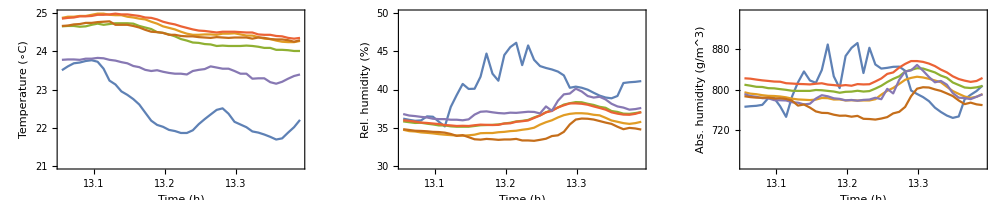

```mathematica
(*Somehow the labelling is wrong?*)
Print["Blue: Above office, Red: Test table east, Green: Test table west, Purple: Test table centre, Orange: Experiment table, Yellow: Laser table"]
Show[pTH,ImageSize->1000]
```